# Integrals For Dummies

## If we can, you can!

Progetto d’esame: Matematica Computazionale & Calcolo Numerico e Software Didattico.

```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

-Graphics- -Graphics- -Graphics- -Graphics-

Autori:

Tommaso Saracchini (email) | Domenico Coriale (email) | Giuseppe De Palma (email) | Eduart Uzier (email)

Per iniziare ad usare questa applicazione ed imparare tutto ciò che serve sugli integrali, devi premere il pulsante START e seguire attentamente le istruzioni illustrate nella prossima slide. Buon divertimento!

Button[-Graphics-,SetDirectory[NotebookDirectory[]];<<"Package.m"; ButtonData→NotebookLocate["Index"];
]

-Graphics-

# Indice

## Primo Livello:

Integrali Definiti

Integrali Indefiniti

## Secondo Livello:

Teorema Fondamentale

Metodi di Risoluzione degli Integrali

## Allenamento:

Esercizi su Integrali Definiti

Esercizi su Integrali Indefiniti

Esercizi Misti

```mathematica
Button[ ImageRotate[-Graphics-,180],ButtonData->NotebookLocate["IndefiniteTheory"];]Button[ImageRotate[-Graphics-,180] ,ButtonData->NotebookLocate["FotoIniziale"]; ]
```

-Graphics- -Graphics-

### Second level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

#### Third level section heading

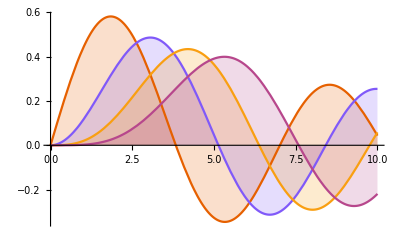

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

# Integrali Definiti

## Introduzione

Che cosa sono gli integrali definiti? E soprattutto: a cosa servono?
In Matematica, cosi` come in Fisica, puo` capitare di dover calcolare l’area che sta sotto ad una curva descritta da una funzione, gli integrali ci permettono di fare proprio questo.
Gli integrali sono lo strumento matematico che serve a calcolare l’area definita dalle curve delle funzioni.
Prendiamo una funzione, come ad esempio quella nell’immagine di sotto, e due punti “a” e “b” sull’asse delle “x” che sono gli estremi dell’intervallo al quale siamo interessati.
Ci chiediamo: come facciamo a calcolare l’area tra la curva , l’asse delle “x” e i due segmenti orizontali dati dalle equazioni delle rette x1=a e x2=b?
Per farlo ci servono gli integrali!

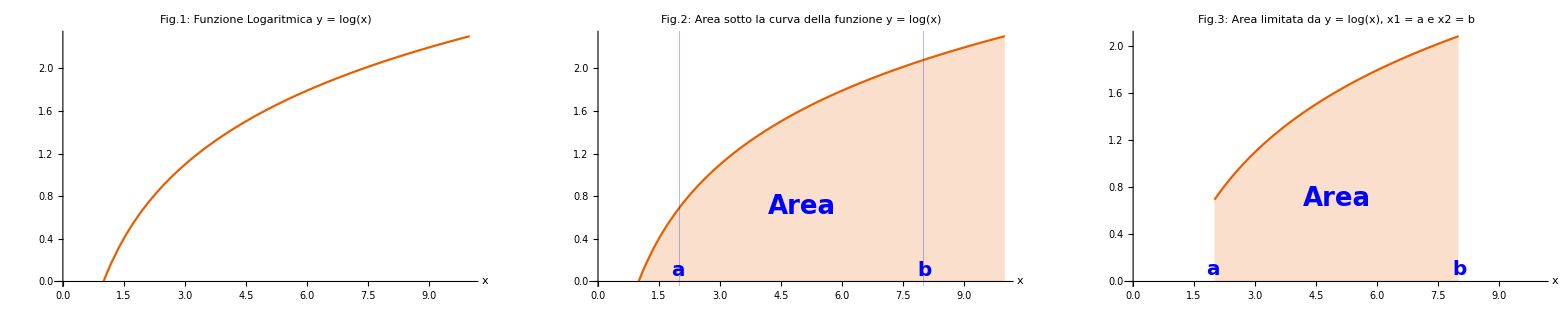

```mathematica
(* definisco i tre punti di rifferimento ossia sinistra, centro e desta*)
align[Right] = {1, 0};
align[Center] = {0, 0}; 
align[Left] = {-1, 0};
(* definisco lo stile del testo che voglio scrivere *)
lText = Text[Style["a", Blue, Bold, FontSize->20], {1.8, 0.1}, align[Left]];
cText = Text[Style["Area", Blue, Bold, Underlined, FontSize->26], {5.0, 0.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {8.2, 0.1}, align[Right]];

txt = Graphics[{lText, cText, rText}];
f[x_]:=Log[x]
(* costruisco i grafi in tre passi diversi *)
plot0=Plot[f[x], {x, 1, 10}, AxesOrigin->{0,0},PlotLabel->Style[Framed["Fig.1: Funzione Logaritmica y =" Log[x]], 22, Bold, Blue, Background->Lighter[Pink]], AxesLabel->Automatic];
plot0; (* la funzione logaritmica nel intervalo [0, 10]*)
plot1=Plot[f[x], {x, 1, 10}, AxesOrigin->{0,0}, Filling->Axis, PlotLabel->Style[Framed["Fig.2: Area sotto la curva della funzione y =" Log[x]], 22, Bold, Blue, Background->Lighter[Pink]], 
GridLines->{{{2, Blue}, {8, Blue}}, None}, PlotRange -> {{0, 10}, All}, AxesLabel->Automatic];
Show[plot1, txt];(* la funzione e i punti x=a e x=b *)
plot2=Plot[f[x], {x, 2, 8}, AxesOrigin->{0,0}, Filling->Axis, PlotLabel->Style[Framed["Fig.3: Area limitata da y = log(x), x1 = a e x2 = b"], 22, Bold, Blue, Background->Lighter[Pink]], 
(*GridLines->{{{2, Blue}, {8, Blue}}, None}*) PlotRange -> {{0, 10}, All}, AxesLabel->Automatic];
(* l'area che vogliamo calcolare *)
GraphicsRow[{plot0, Show[plot1, txt], Show[plot2,txt]}]
```

## Andiamo per passi...

Prendiamo una funzione semplice (la funzione costante): una retta che sia parallela all’asse delle “x” (ad esempio la retta di equazione y = 4).
Siamo interessati a calcolare nell’intervallo tra x = 1 e x = 3 come in figura, come facciamo?

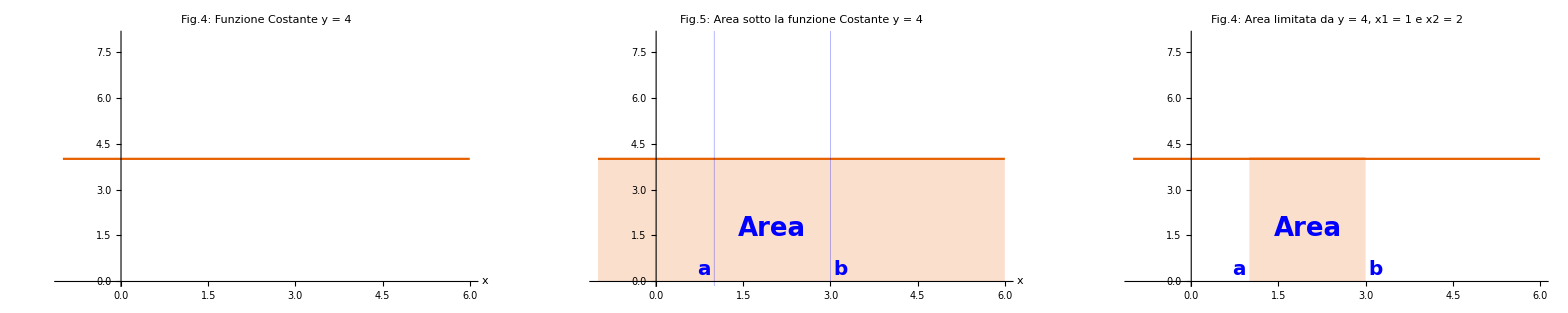

```mathematica
lText = Text[Style["a", Blue, Bold, FontSize->20], {0.7, 0.4}, align[Left]];
cText = Text[Style["Area", Blue, Bold, Underlined, FontSize->26], {2.0, 1.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {3.3, 0.4}, align[Right]];

txt2 = Graphics[{lText, cText, rText}];
funlim1 = -1;
funlim2 = 6;
f[x_]:=4
plot3=Plot[f[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.4: Funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic];
plot4=Plot[y=4, {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.5: Area sotto la funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], Filling->Axis, GridLines->{{{1, Blue}, {3, Blue}}, None},
AxesOrigin->{0,0}, AxesLabel->Automatic];
(*Plot[y=4, {x, 1, 3}, PlotLabel->Style[Framed["Fig.4: Funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], Filling->Axis, GridLines->{{{1, Blue}, {3, Blue}}, None}, 
AxesOrigin->{0,0}, AxesLabel->Automatic]*)
inlimit1 = 1;
inlimit2 = 3;
(*f[x_] = 100 - 8*x^2 + x^3;*)
g1 = Plot[f[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.4: Area limitata da y = 4, x1 = 1 e x2 = 2"], 22, Bold, Blue, Background->Lighter[Pink]]];
g2 = Plot[f[x], {x, inlimit1, inlimit2}, 
   Filling -> 0];
GraphicsRow[{plot3, Show[plot4, txt2], Show[g1, g2, txt2]}]
```

Semplice : E' un rettangolo!!! Sapendo che il rettangolo dato ha base 2 ed altezza 4 l' area sara 8.
Quindi diciamo che l' INTEGRALE da 1 a 3 della funzione f (x) = 4 in dx e' uguale a 8! Facile no?! In simboli ∫_1^3 f(x)ⅆx = 8
Ti stai chiedendo cose’ dx? Lo scopriamo tra poco...! Intanto facciamo un altro semplice esempio.

Clica sul Rettangolo

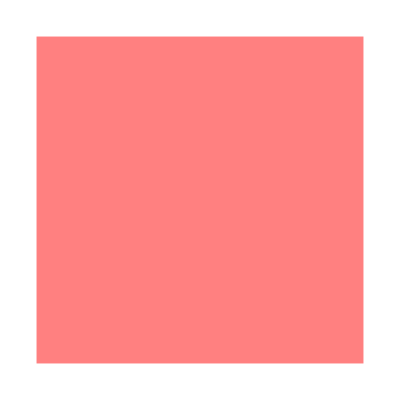

```mathematica
Print["Clica sul Rettangolo"]
PopupWindow[Graphics[{Pink, Rectangle[],ImageSize->Small}],"L'Area di un Rettangolo e' data dal prodotto della sua base b con la sua altezza h: A = b * h"]
```

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.